```mathematica
Take[QuadrilateralsWithPattern[7,1],1]
```

{{{1,3},{2,6},{4,7},{5}}}

```mathematica
ShowGraphs[list_,frameStyle_]:=Map[
Block[{sym=SymbolToSets[#]},
Labeled[Framed[GraphFromSymbol[#],FrameStyle->frameStyle[SymbolToSets[#]]],SetsToLabel2[sym]]
]&,
list
]
```

```mathematica
CountEdges[list_]:=Block[{result={},tot},
tot=Total[Table[If[(el[[1]]≤5)≠(el[[2]]≤5),AppendTo[result,el];1,0],{el,list}]];
tot
]
```

```mathematica
Table[
First[Map[CountEdges[EdgeList[GraphComplement[GraphFromSets[#]]]]&,Take[QuadrilateralsWithPattern[k,1],1]]],{k,5,14}]
```

{0,1,2,3,5,6,7,8,10,11}

```mathematica
Length[QuadrilateralsWithPattern[13,1]]
```

65536

```mathematica
FactorInteger[65536]
```

{{2,16}}

```mathematica
FactorInteger[262144]
```

{{2,18}}

```mathematica
2^20
```

1048576

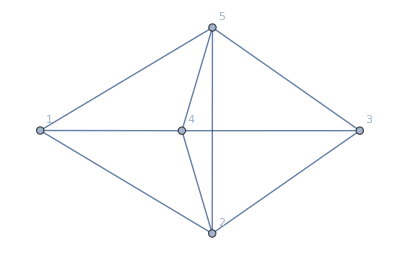
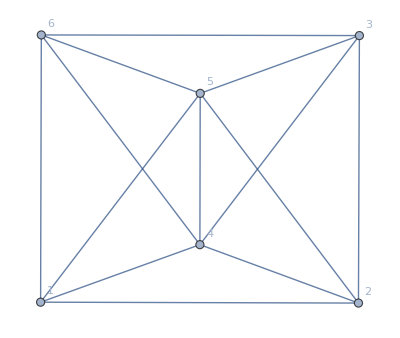
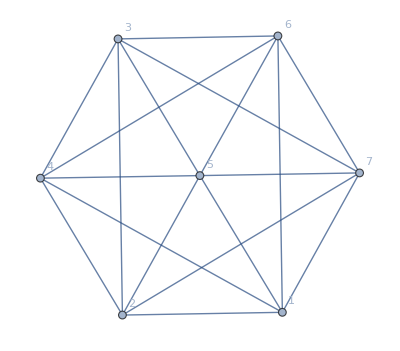
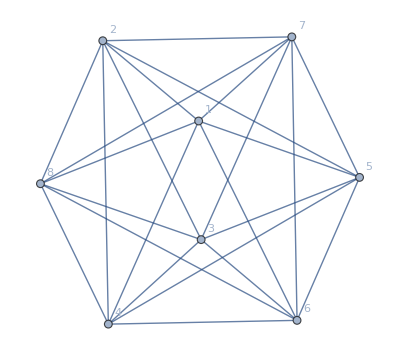
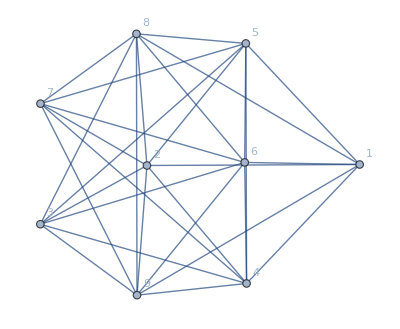
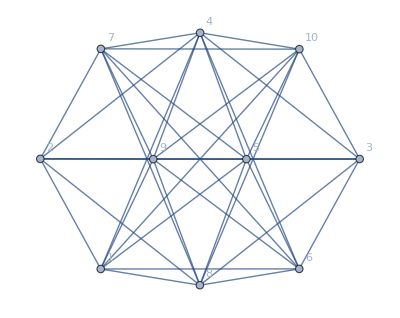
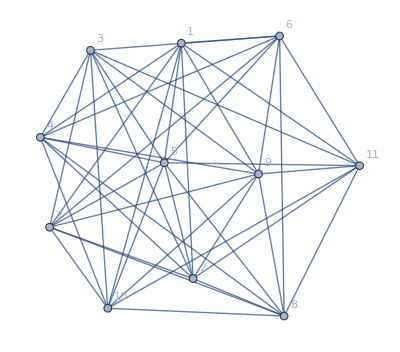
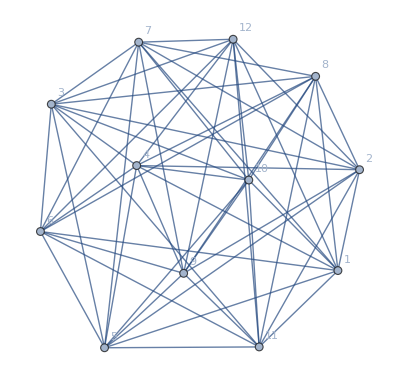

```mathematica
Table[
First[Map[Graph[GraphFromSets[#],VertexLabels->"Name"]&,Take[QuadrilateralsWithPattern[k,1],1]]],{k,5,14}]
```

```mathematica
CoordinatesForNodes[nodes_]:=Table[
If[i≤5,
{2i,((i-3)^2/3)},
{2(i-(nodes/2)),1/nodes (-6+nodes)^2}
]
,{i,1,nodes}]
```

```mathematica
CoordinatesForNodes[nodes_]:=Table[
If[i≤5,
{2i,((i-3)^2/3)},
{2(i-(nodes/2)),10-((i-6-(nodes-6)/2)^2/3)}
]
,{i,1,nodes}]
```

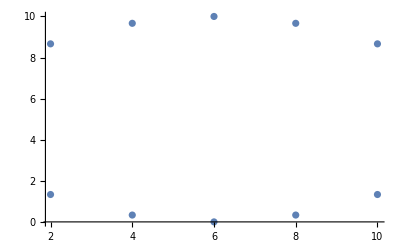

```mathematica
CoordinatesForNodes[10]//ListPlot
```